```mathematica
n=10;
λ=500*^-9;
k=(2 π)/λ;
f=10*^-3;
d=8*^-3;
ri=1.5;
α=ArcSin[d/(2 f)];
NA=ri Sin[α]
min=-f Sin[α];max=f Sin[α];
zmin=-f;zmax=f;
step = 200; zstep=200;
l0=1;
A = (π f l0)/λ;
β=2;
u[z_]:=k z Sin[α]^2;
v1d=Abs[Table[{k Sin[α] Range[min,max,(max-min)/step],z},{z,Range[zmin,zmax,(zmax-zmin)/zstep]}]];
apod[θ_]:=Exp[-β^2 (Sin[θ]/Sin[α])^2] BesselJ[1,2 β Sin[θ]/Sin[α]];
```

0.6

```mathematica
N[α]
```

0.411517

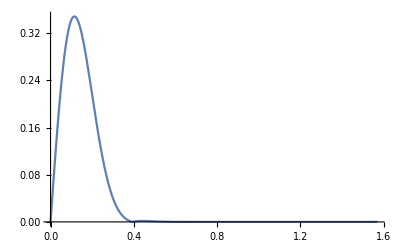

```mathematica
Plot[Abs[apod[x]],{x,0,Pi/2},PlotRange->All]
```

```mathematica
normapod[θ_]:=l0/NIntegrate[apod[x],{x,0,Pi/2}] Exp[-β^2 (Sin[θ]/Sin[α])^2] BesselJ[1,2 β Sin[θ]/Sin[α]];
```

```mathematica
(*Trapezoid Rule*)
RHO1d=Z1d=PHI1d=0*v1d;
RHO1d[[All,2]]=Z1d[[All,2]]=PHI1d[[All,2]]=v1d[[All,2]];
For[i=1,i<n,i++,RHO1d[[All,1]]=RHO1d[[All,1]]+(√Cos[i α/n]*Sin[2 i α/n]*normapod[i α/n]*BesselJ[1,v1d[[All,1]] Sin[i α/n]/Sin[α]] *Exp[I u[RHO1d[[All,2]]] Cos[i α/n]/Sin[α]^2]);
Z1d[[All,1]]=Z1d[[All,1]]+(√Cos[i α/n]*Sin[i α/n]^2*normapod[i α/n]*BesselJ[0,v1d[[All,1]] Sin[i α/n]/Sin[α]]* Exp[I u[Z1d[[All,2]]] Cos[i α/n]/Sin[α]^2]);PHI1d[[All,1]]=PHI1d[[All,1]]+(√Cos[i α/n]* Sin[i α/n]*Cos[2 i α/n]*normapod[i α/n]*BesselJ[1,v1d[[All,1]] Sin[i α/n]/Sin[α]]*Exp[I u[PHI1d[[All,2]]] Cos[i α/n]/Sin[α]^2])];
RHO1d[[All,1]]=A α/n(RHO1d[[All,1]]+0.5*(√Cos[α]*Sin[2 α]*normapod[α]*BesselJ[1,v1d[[All,1]]] *Exp[I u[RHO1d[[All,2]]] Cos[α]/Sin[α]^2]));
Z1d[[All,1]]=2 I A α/n(Z1d[[All,1]]+0.5*(√Cos[α]*Sin[α]^2*normapod[α]*BesselJ[0,v1d[[All,1]]]* Exp[I u[Z1d[[All,2]]] Cos[α]/Sin[α]^2 ]));
PHI1d[[All,1]]=2A α/n(PHI1d[[All,1]]+0.5*(√Cos[α]* Sin[α]*Cos[2α]*normapod[α]*BesselJ[1,v1d[[All,1]]]*Exp[I u[PHI1d[[All,2]]] Cos[α]/Sin[α]^2]));
```

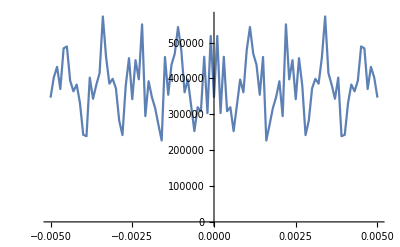

```mathematica
list=RHO1d[[All,1]]*0;
For[j=1,j≤Length[RHO1d[[All,1]]],j++,list[[j]]=Integrate[Interpolation[Abs[RHO1d[[j,1]]^2],InterpolationOrder->1][x],{x,1,Length[RHO1d[[j,1]]]}]];
ListLinePlot[list,DataRange->{zmin,zmax}]
```

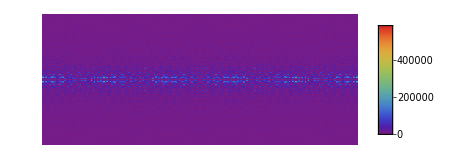

```mathematica
ArrayPlot[Abs[Transpose[RHO1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

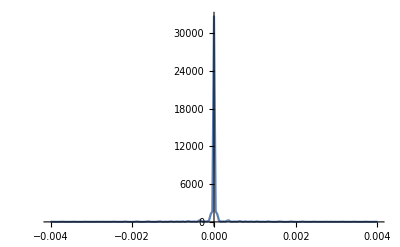

```mathematica
ListLinePlot[Abs[Z1d[[51,1]]]^2,DataRange->{min,max},PlotRange->All]
```

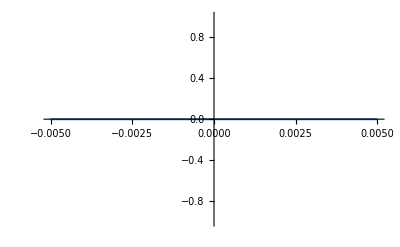

```mathematica
list=Z1d[[All,1]]*0;
For[j=1,j≤Length[Z1d[[All,1]]],j++,list[[j]]=Integrate[Interpolation[Abs[Z1d[[j,1]]^2],InterpolationOrder->1][x],{x,1,Length[Z1d[[j,1]]]}]];
ListLinePlot[list,DataRange->{zmin,zmax}]
```

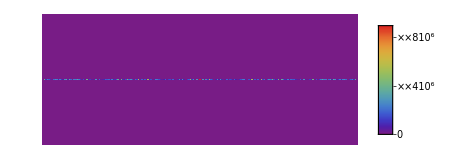

```mathematica
ArrayPlot[Abs[Transpose[Z1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
(*Manipulate[ListLinePlot[Abs[RHO1d[[z,1]]]^2+Abs[Z1d[[z,1]]]^2,DataRange->{min,max},PlotRange->All],{z,1,101,1}]*)
```

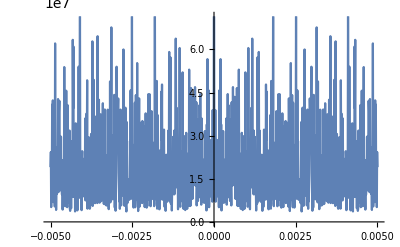

```mathematica
list=Z1d[[All,1]]*0;
For[j=1,j≤Length[Z1d[[All,1]]],j++,list[[j]]=Integrate[Interpolation[Abs[Z1d[[j,1]]]^2+Abs[RHO1d[[j,1]]]^2,InterpolationOrder->1][x],{x,1,Length[Z1d[[j,1]]]}]];
ListLinePlot[list,DataRange->{zmin,zmax}]
```

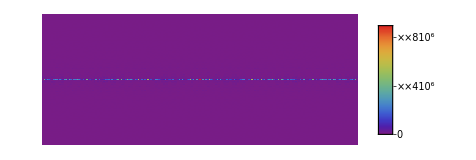

```mathematica
ArrayPlot[Abs[Transpose[RHO1d[[All,1]]]]^2+Abs[Transpose[Z1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
(*Manipulate[ListLinePlot[Abs[PHI1d[[z,1]]]^2,DataRange->{min,max},PlotRange->All],{z,1,101,1}]*)
```

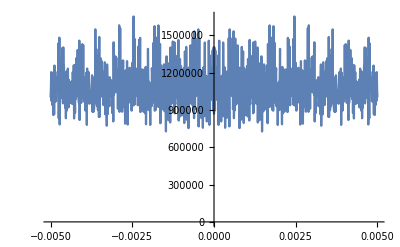

```mathematica
list=PHI1d[[All,1]]*0;
For[j=1,j≤Length[PHI1d[[All,1]]],j++,list[[j]]=Integrate[Interpolation[Abs[PHI1d[[j,1]]^2],InterpolationOrder->1][x],{x,1,Length[PHI1d[[j,1]]]}]];
ListLinePlot[list,DataRange->{zmin,zmax}]
```

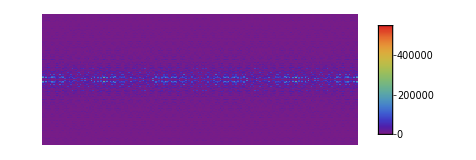

```mathematica
ArrayPlot[Abs[Transpose[PHI1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```